# Fourier sine transform

```mathematica
Needs["FourierSeries`"]
```

```mathematica
Clear["Global`*"]
```

## Fourier sine transform

```mathematica
f[t_]:=ⅇ^(-2 t^2)
```

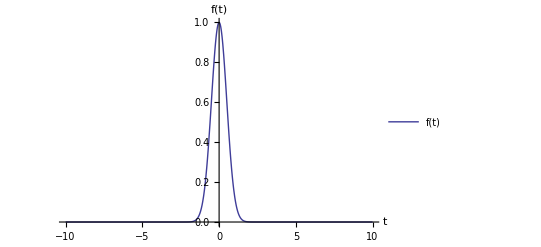

```mathematica
Plot[f[t],{t,-10,10}, PlotRange -> All,PlotLegends->"Expressions",AxesLabel->{"t","f(t)"}]
```

```mathematica
F[ω_]=FourierSinTransform[f[t], t,ω]
```

DawsonF[ω/(2 √2)]/(√π)

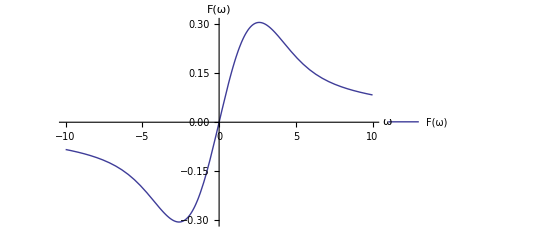

```mathematica
Plot[F[ω],{ω,-10,10}, PlotRange -> All,PlotLegends->"Expressions",AxesLabel->{"ω","F(ω)"}]
```

## Inverse Fourier sine transform

```mathematica
InverseFourierSinTransform[F[ω],ω,t]
```

ⅇ^(-2 t^2)